RHS=(k1-i k2
i k3-k4 m
k5 m-k6 p)

Sample constraints: {s1||s2||s3,!s1,True,s2⇒s1,True}

{}

Check siphons={}

Invariant facets are:

there is 1 fixed pts

{{i→k1/k2,m→(k1 k3)/(k2 k4),p→(k1 k3 k5)/(k2 k4 k6)}}

(0)

eigs of K are{0}

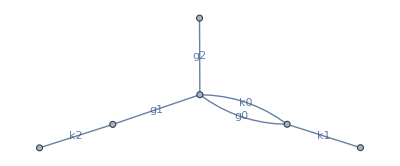

```mathematica
(*1: First steps*)
ClearAll["Global‘*"]
SetDirectory[NotebookDirectory[]];SetOptions[$FrontEndSession, NotebookAutoSave -> True];
NotebookSave[];
AppendTo[$Path, FileNameJoin[{$HomeDirectory, "Dropbox", "EpidCRNmodels"}]];<<EpidCRN`;
RN={0 -> "i", "i"-> 0 ,
       "i"->  "i"+"m", "m"->  0,
      "m"->"p"+"m", "p"->  0}; rates={k0,g0,k1,g1,k2,g2};
{RH,spe}=reaToRHS[RN];var=ToExpression[spe];
RHS = RH /. Thread[spe -> var];Print["RHS=",RHS//MatrixForm];
par=Par[RHS,var];cp=Thread[par>0];cv=Thread[var>=0];ct=Join[cp,cv];
mS=minSiph[spe,asoRea[RN]]
Print["Check siphons=",isSiph[ToString/@var,asoRea[RN],#]&/@mS]
(*Find all invariant facets*)
iF=invFacet[RN,3];
Print["Invariant facets are:"];
Do[Print[iF[[i]]],{i,Length[iF]}];
eq=Thread[RHS==0];eqp=Join[eq,ct];
so=reCL[Solve[eqp,var]/. Subscript[EpidCRN`Private`k, n_] :> Subscript[k, n]];
Print["there is ",so//Length," fixed pts"]
so
mod={RHS,var,par};
inf={3};
ng=NGM[mod,inf];M=ng[[1]];
K=ng[[6]]/. Subscript[EpidCRN`Private`k, n_] :> Subscript[k, n];K//MatrixForm
Print[" eigs of K are",K//Eigenvalues]
Needs["ReactionKinetics`"];
ShowFHJGraph[RN,rates]
```

```mathematica
reacD=ReactionsData[RN];
Γ= reacD["γ"]//Normal;Γ//MatrixForm;
expo= reacD["α"]//Normal//Transpose;
{comp,r,nR,spec,nS,vol,vars,defi}=reacD["complexes","reactionsteps","R","species","M","volpertgraph",
"variables","deficiency"];
spec;Print["rates are product of",
rv=expM[var,expo]," and ",
tk=rates];
Rv=tk*rv;
RHS=Γ.Rv//Simplify;
Print["RHS ",RHS//MatrixForm]
par=Par[RHS,var];cp=Thread[par>0];cv=Thread[var>=0];
ct=Join[cp,cv];
jac=Grad[RHS,var];
defi
```

rates are product of{1,i,i,m,m,p} and {k0,g0,k1,g1,k2,g2}

RHS (-g0 i+k0
i k1-g1 m
k2 m-g2 p)

δ=N-L-S=6-1-3=2